```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adityak/Aditya/git/root_tracking/Mathematica/SRSPM/Singularity_event

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

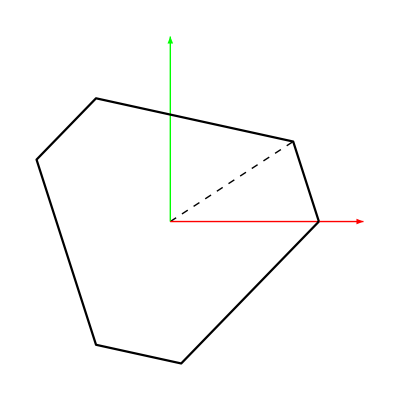

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

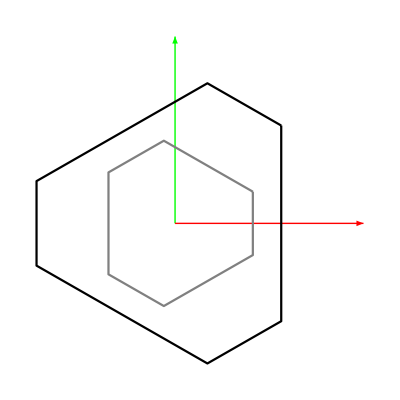

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{0.732576,0.680685,0},{0.223203,0.974772,0},{-0.955779,0.294087,0},{-0.955779,-0.294087,0},{0.223203,-0.974772,0},{0.732576,-0.680685,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→0.732576,a1y→0.680685,a1z→0,a2x→0.223203,a2y→0.974772,a2z→0,a3x→-0.955779,a3y→0.294087,a3z→0,a4x→-0.955779,a4y→-0.294087,a4z→0,a5x→0.223203,a5y→-0.974772,a5z→0,a6x→0.732576,a6y→-0.680685,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
rootsC = ({{x->1.8700438348728161, y->-0.5235870043873335, z->0.-0.926898973258719 ⅈ, c1->0.-0.10569096861540776 ⅈ, c2->0.+0.7154784037290103 ⅈ, c3->0}, {x->1.8700438348728161, y->-0.5235870043873335, z->0.+0.926898973258719 ⅈ, c1->0.+0.10569096861540776 ⅈ, c2->0.-0.7154784037290103 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.-0.9685245785328371 ⅈ, c1->0.-0.6638886705593215 ⅈ, c2->0.-0.3422565386596551 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.+0.9685245785328371 ⅈ, c1->0.+0.6638886705593215 ⅈ, c2->0.+0.3422565386596551 ⅈ, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.-1.3894731322781502 ⅈ, c1->0.+0.6338547336758182 ⅈ, c2->0.-0.42758251604766423 ⅈ, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.+1.3894731322781502 ⅈ, c1->0.-0.6338547336758182 ⅈ, c2->0.+0.42758251604766423 ⅈ, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
initpose=Join[qx/.roots[[2]],iksolC[qx/.roots[[2]]]];
initposes=Table[Join[qx/.roots[[ii]],iksolC[qx/.roots[[ii]]]],{ii,8}];
initposeC = Join[qx/.rootsC[[1]],iksolC[qx/.rootsC[[1]]]];
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→0.628916,yt1→-0.430149,zt1→0.91962},{xt2→0.449784,yt2→-0.557918,zt2→0.245515},{xt3→0.127107,yt3→-0.844307,zt3→0.153522},{xt4→-0.212447,yt4→-1.17689,zt4→0.679753},{xt5→-0.101009,yt5→-1.09741,zt5→1.09912},{xt6→0.417678,yt6→-0.637052,zt6→1.24699}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→0.732576,yb1→0.680685,zb1→0},{xb2→0.223203,yb2→0.974772,zb2→0},{xb3→-0.955779,yb3→0.294087,zb3→0},{xb4→-0.955779,yb4→-0.294087,zb4→0},{xb5→0.223203,yb5→-0.974772,zb5→0},{xb6→0.732576,yb6→-0.680685,zb6→0}}

```mathematica
roots[[1]]
```

{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→8/11,yb1→11/16,zb1→0},{xb2→2/9,yb2→28/29,zb2→0},{xb3→-19/20,yb3→2/7,zb3→0},{xb4→-19/20,yb4→-2/7,zb4→0},{xb5→2/9,yb5→-29/30,zb5→0},{xb6→8/11,yb6→-13/19,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Compiled functions

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
qfull = Join[qx, qvar];
```

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
Jηext//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

## Plotting the SRSPM:

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]]]
```

-Graphics3D-

## Path generation

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

```mathematica
scale = 0.2;
```

```mathematica
(* Circular path with changing orientation *)
parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]};
```

```mathematica
(* Circular path with constant orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0}; *)
```

```mathematica
(* Straight line path moving towards singularity *)
(* parampath = {scale-α,α, 1.28-α, scale*1, scale*0,scale*0}; *)
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
pathplt=Graphics3D[{Red, Sphere[Chop[pathpts[[;;]]][[;;, ;;3]], 0.025]}]
```

-Graphics3D-

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
legvals[[1]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
initpose=Join[pathpts[[1]], iksolC[pathpts[[1]]]]
```

{0.2,0.,1.28,0.2,0.,0.,0.00305624-8.22748×10^-17 ⅈ,-0.0668855-2.77949×10^-17 ⅈ,0.456963-1.1835×10^-16 ⅈ,0.546956-1.39651×10^-17 ⅈ,-0.0946901-1.93388×10^-16 ⅈ,0.00349011-1.87171×10^-16 ⅈ,0.336276+1.47256×10^-17 ⅈ,0.286891-5.66207×10^-17 ⅈ,-0.0210274-2.43773×10^-17 ⅈ,0.0247844-1.74336×10^-16 ⅈ,-0.395383-1.37395×10^-16 ⅈ,-0.379795-1.10578×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
(*legvals//MatrixForm*)
(*legvals//Im//Flatten//CForm*)
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

## Newton-Raphson method for root tracking

## Real roots:

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[(Norm[nvec]≥ 10^-10)&&(loopcounter≤100),
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Jηext//Dimensions
Jηext//Variables
```

{18,18}

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

### Root 1:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[1,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.54665×10^-15

```mathematica
(* Function to track a particular root given a table of the leg lengths for the entire path. *)
TrackPathRoot[initpose_,legvals_,steps_]:=
Module[{rtempϕ,rϕlist,ii},
rtempϕ = initpose;
rϕlist = {rtempϕ};
For[ii=2,ii≤steps, ii++, 
rtempϕ = NRTracking[legvals[[ii]], rtempϕ, cηext, cJηext];
AppendTo[rϕlist, rtempϕ];
];
Return[rϕlist];
]
```

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r1tempϕ = initposes[[1,;;-7]];
tic[]
r1ϕlist = TrackPathRoot[r1tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02697 seconds.

CPU time consumed: 0.026984 seconds.

```mathematica
r1xlist = r1ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 2:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[2,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.22299×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r2tempϕ = initposes[[2,;;-7]];
tic[]
r2ϕlist = TrackPathRoot[r2tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.019 seconds.

CPU time consumed: 0.019013 seconds.

```mathematica
r2xlist = r2ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r2trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r2xlist[[u]], iksolC[r2xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r2xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r2xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 3:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[3,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.11426×10^-15

```mathematica
Length[legvals]
```

51

```mathematica
initposes[[3,;;-7]]
```

{-0.513695,-0.519996,-0.798723,-0.333759,-0.951699,0,-1.88547-1.05103×10^-16 ⅈ,-2.65366+2.74726×10^-17 ⅈ,2.78228+1.86009×10^-17 ⅈ,2.89251-1.51877×10^-16 ⅈ,-2.20522+5.34046×10^-17 ⅈ,-1.74294-1.42102×10^-16 ⅈ,0.61606-1.17742×10^-16 ⅈ,0.697469-2.13889×10^-16 ⅈ,0.419763+1.94314×10^-17 ⅈ,0.5377-1.52741×10^-16 ⅈ,0.0705025-6.62747×10^-17 ⅈ,-0.103948+3.0597×10^-18 ⅈ}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r3tempϕ = initposes[[3,;;-7]];
tic[]
r3ϕlist = TrackPathRoot[r3tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02894 seconds.

CPU time consumed: 0.028966 seconds.

```mathematica
r3xlist = r3ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r3trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r3xlist[[u]], iksolC[r3xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r3xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r3xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 4:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[4,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.20587×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r4tempϕ = initposes[[4,;;-7]];
tic[]
r4ϕlist = TrackPathRoot[r4tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02762 seconds.

CPU time consumed: 0.027622 seconds.

```mathematica
r4xlist = r4ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r4trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r4xlist[[u]], iksolC[r4xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r4xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r4xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 5:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[5,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.66454×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r5tempϕ = initposes[[5,;;-7]];
tic[]
r5ϕlist = TrackPathRoot[r5tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02044 seconds.

CPU time consumed: 0.020434 seconds.

```mathematica
r5xlist = r5ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r5trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r5xlist[[u]], iksolC[r5xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r5xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r5xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 6:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[6,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.097×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r6tempϕ = initposes[[6,;;-7]];
tic[]
r6ϕlist = TrackPathRoot[r6tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.02733 seconds.

CPU time consumed: 0.027324 seconds.

```mathematica
r6xlist = r6ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r6trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r6xlist[[u]], iksolC[r6xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r6xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r6xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 7:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[7,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.47006×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r7tempϕ = initposes[[7,;;-7]];
tic[]
r7ϕlist = TrackPathRoot[r7tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.026 seconds.

CPU time consumed: 0.026021 seconds.

```mathematica
r7xlist = r7ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r7trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r7xlist[[u]], iksolC[r7xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r7xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r7xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 8:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[8,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.28805×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
r8tempϕ = initposes[[8,;;-7]];
tic[]
r8ϕlist = TrackPathRoot[r8tempϕ,legvals,Length[legvals]];
toc[]
```

Actual time consumed: 0.0265 seconds.

CPU time consumed: 0.026516 seconds.

```mathematica
r8xlist = r8ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r8trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r8xlist[[u]], iksolC[r8xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r8xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r8xlist], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

## Singularity manifold

```mathematica
g11 = Import["singmanifold_ddp_cords_0_2_0_0_0_0.m"]
```

-8.76498×10^-15+y^2 (1.7087×10^-14-0.0317581 z)+x^2 (9.22743×10^-15-1.73472×10^-18 z)+0.0364021 z-3.56473×10^-14 z^2-0.381097 z^3+x (-4.84335×10^-15+y (-0.0100837+5.59691×10^-14 z)+0.0671749 z-2.09902×10^-13 z^2)+y (0.00732243-1.11494×10^-13 z+0.23501 z^2)

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->{Green,Opacity[0.6]},PlotPoints->60];
```

```mathematica
xpose = {0.2,0,1.28,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp,pathplt]
```

-Graphics3D-

### Checking if Det[Jηext] is 0 for random points on g11

```mathematica
randomnumbers=500;
xrandom=RandomReal[{-1.6,1.6},randomnumbers];
yrandom=RandomReal[{-1.6,1.6},randomnumbers];
zrandom=Table[z/.Solve[(g11/.Inner[Rule,{x,y},{xrandom[[ii]],yrandom[[ii]]},List])==0],{ii,randomnumbers}];
ptsrandom=Flatten[Table[Table[{xrandom[[ii]],yrandom[[ii]],zrandom[[ii]][[jj]]},{jj,3}],{ii,randomnumbers}],1];
randrule=Table[Inner[Rule,{x,y,z},ptsrandom[[ii]],List],{ii,randomnumbers}];
```

```mathematica
(* Checking if the obtained points lie on g11=0 *)
Table[g11/.randrule[[ii]],{ii,randomnumbers}]//Abs//Max
```

1.45717×10^-16

```mathematica
(* Checking if the random configurations satisfy the constraints *)
Table[Norm[cηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}]//Max
```

2.58902×10^-15

```mathematica
(* Now evaluating Det[Jηext] for these random points *)
randomDet=Table[Det[cJηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}];
randomDet//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.02234×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Singularity Event Identification

```mathematica
(* Specify one branch of interest on which we are moving and try to warn if the branch will encounter a singularity. Also, try to locate the singularity (estimate it with reasonable accuracy) *)
```

```mathematica
(* finddistroots[allroots,intrestroot,qxORqfull]: Function to find the distance between the branch of interest and other branches *)
(* Description of the inputs:
	allroots - qfull for all the branches, at a particular instant
  intrestroot - The branch in which the manipulator is physically moving
	qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
finddistroots[allroots_,intrestroot_,qxORqfull_]:=
Module[{n,ii,dist},
n=Length[allroots];
dist={};
For[ii=1,ii≤n,ii++,
If[ii≠intrestroot,
If[qxORqfull==1,
(* True *)AppendTo[dist,Norm[allroots[[intrestroot]]-allroots[[ii]]]];,
(* False *)AppendTo[dist,Norm[(allroots[[intrestroot]]-allroots[[ii]])[[1;;6]]]];
];
];
];
Return[dist]
];
```

```mathematica
(* Function to find the coefficients to the fitting quadratic function, which will be used to estimate the singularity *)
(* Description of the inputs:
	xlist - A list of 3 values of the path parameter (input variable)
  ylist - A list of the corresponding 3 values of the distance (output variable) 
*)
(* Description of the output:
{a1,a2,a3} - The coefficients of the quadratic equation which is satisfied by the 3 input points. 
          Equation of the form a1*α^2+a2*α+a3=d where α is the input variable and d is the output variable. 
*)
findextrapfuncCoeff[xlist_,ylist_]:=
Module[{a1,a2,a3,eq,x,y,coeff},
eq=a1*x^2+a2*x+a3-y;
coeff=Solve[{(eq/.Inner[Rule,{x,y},{xlist[[1]],ylist[[1]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[2]],ylist[[2]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[3]],ylist[[3]]},List])}=={0,0,0},{a1,a2,a3}];
Return[Flatten[{a1,a2,a3}/.coeff]];
];
```

```mathematica
NRallbranches[allbranches_,legvals_]:=
Module[{},
Return[Table[Join[NRTracking[legvals, allbranches[[ii]][[1;;18]], cηext, cJηext],legvals],{ii,Length[allbranches]}]]
];
```

```mathematica
Clear[intrestbranch,distroots,cnt,alphaI,alphaIminus1,alphaIminus2,alphaIplus1,distI,distIminus1,distIminus2,deldist,delalpha,predstep,grad,singbranch,dvals,alphavals,extrapcoeff,extrapfunc,solSing,estiqxSing,estialphaSing,estiqfullSing,singFlag]
```

```mathematica
(* Function to identify if a singularity is being encountered along the desired path. *)
(* Description of the inputs:
	allbranches - A table of qfull for all the branches, along the entire path
    intrestbranch - The branch in which the manipulator is physically moving
	pathparam - (α,initval,finalval,initstepsize)
	parampath - Path definition: The task space variables defined in terms of the path parameter
 qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
singularityEventIdentifier[allbranches_,intrestbranch_,pathparam_,parampath_,qxORqfull_]:=
Module[{α,initval,finalval,stepsize,distroots,prevstep,cnt,alphaI,alphaIminus1,alphaIminus2,alphaIplus1,distI,distIminus1,distIminus2,deldist,delalpha,legvals,nextstep,predstep,grad,ii,singbranch,dvals,alphavals,extrapcoeff,extrapfunc,a1,a2,a3,solSing,estiqxSing,estialphaSing,estiqfullSing,singFlag,returnval,checkalpha},
(* Defining a vector to store the distance between the branch of intrest and other branches *)
distroots={};
prevstep=allbranches;
{α,initval,finalval,stepsize}=pathparam;
(* At cnt=1, *)
alphaIminus1=initval;
alphaIminus2=initval;
(* Using only the task space variable to find the distance between the roots *)
distIminus1=finddistroots[prevstep,intrestbranch,qxORqfull];
distIminus2=distIminus1;
singFlag=0;
If[stepsize>0,checkalpha=alphaIminus1<finalval;,checkalpha=alphaIminus1>finalval;];
While[singFlag==0&&checkalpha,
If[stepsize>0,checkalpha=alphaIminus1<finalval;,checkalpha=alphaIminus1>finalval;];
alphaI=alphaIminus1+stepsize;
If[checkalpha,alphaIplus1=alphaI+stepsize,alphaIplus1=finalval];
delalpha=alphaI-alphaIminus1;
legvals=iksolC[parampath/.{α->alphaI}][[-6;;]];
nextstep=NRallbranches[prevstep,legvals];
distI=finddistroots[nextstep,intrestbranch,0];
deldist=distI-distIminus1;
grad=Table[deldist[[ii]]/delalpha,{ii,1,Length[distI]}];
predstep=Table[distI[[ii]]+(alphaIplus1-alphaI)*grad[[ii]],{ii,1,Length[grad]}];
For[ii=0,ii≤Length[predstep],ii++,
If[predstep[[ii]]<0,
singFlag=1;
singbranch=ii;
Print["Singularity encountered, branches ",intrestbranch," and ",singbranch," are observed to merge."];
dvals={distIminus2[[singbranch]],distIminus1[[singbranch]],distI[[singbranch]]};
alphavals={alphaIminus2,alphaIminus1,alphaI};
extrapcoeff=findextrapfuncCoeff[alphavals,dvals];
extrapfunc=a1*α^2+a2*α+a3/.Inner[Rule,{a1,a2,a3},extrapcoeff,List];
solSing=Solve[extrapfunc==0,α];
estialphaSing=If[Abs[(α/.solSing[[1]])-alphaI]<Abs[(α/.solSing[[2]])-alphaI],solSing[[1]],solSing[[2]]];
estiqxSing=parampath/.estialphaSing;
estiqfullSing=Join[estiqxSing,iksolC[estiqxSing]];
returnval={singFlag,estialphaSing,singbranch,estiqfullSing};
];
];
If[singFlag==0,
alphaIminus2=alphaIminus1;
alphaIminus1=alphaI;
prevstep=nextstep;
If[alphaIminus1==finalval,
returnval={0,Null,Null};
Print["No singularity encountered"]
];
distIminus2=distIminus1;
distIminus1=distI;,
Break;
];
];
Return[returnval];
];
```

## Locating the singularity for different type of paths

## Straight Line Path

### Defining the path

```mathematica
(* Straight line path moving towards singularity *)
parampath = {scale-α,α, 1.28-α, scale*1, scale*0,scale*0}; 
pathparam={α,0,π/3,π/150};
legvals = Table[iksolC[(parampath/.{α->ii})][[-6;;]],{ii,0,π/3,π/150}];
desiredpath=Table[(parampath/.{α->ii}),{ii,0,π/3,π/150}];
desiredpathplt=Graphics3D[{Blue,Thick,Line[desiredpath[[;;44,1;;3]]]},Boxed->False];
```

### Actual point of singularity along the path:

```mathematica
(* The value of path parameter when the path hits the singularity manifold *)
alphaSing=Solve[Expand[g11/.Inner[Rule,{x,y,z},parampath[[1;;3]],List]]==0,α]
```

{{α→0.798115},{α→1.16642-0.248537 ⅈ},{α→1.16642+0.248537 ⅈ}}

```mathematica
(* Task space configuration at the singularity *)
qxSing=parampath/.alphaSing[[1]]
```

{-0.598115,0.798115,0.481885,0.2,0.,0.}

```mathematica
(* The Active and passive joint parameters at the singularity *)
qfullSing=Join[qxSing,iksolC[qxSing]]//Chop
```

{-0.598115,0.798115,0.481885,0.2,0,0,-0.950867,-0.906905,-0.163079,-0.286329,-1.28847,-1.10707,-0.317943,-0.30101,-0.924925,-1.13072,-0.925127,-0.962679,1.02693,1.19475,1.04099,0.845481,1.55504,1.55375}

```mathematica
(* Verifying that the obtained point is indeed singular *)
cJηext@@qfullSing//Det
```

-4.27926×10^-14+0. ⅈ

### Using extrapolation strategy to estimate the location of the singularity

```mathematica
singularityEventIdentifier[Chop[initposes],2,pathparam,parampath,0]
```

Singularity encountered, branches 2 and 3 are observed to merge.

{1,{α→0.798119},3,{-0.598119,0.798119,0.481881,0.2,0.,0.,-0.950873-1.30916×10^-16 ⅈ,-0.90691+5.79332×10^-18 ⅈ,-0.163087-1.23004×10^-16 ⅈ,-0.286345-1.0966×10^-16 ⅈ,-1.28847-1.77084×10^-16 ⅈ,-1.10708-5.4969×10^-17 ⅈ,-0.317947-1.52816×10^-16 ⅈ,-0.301013-1.5174×10^-16 ⅈ,-0.92493-1.07001×10^-16 ⅈ,-1.13072-3.88047×10^-17 ⅈ,-0.925127-1.26895×10^-16 ⅈ,-0.96268-4.25309×10^-17 ⅈ,1.02693+0. ⅈ,1.19475+0. ⅈ,1.04099+0. ⅈ,0.845484+0. ⅈ,1.55505+0. ⅈ,1.55375+0. ⅈ}}

```mathematica
(* Verifying that the "singularityEventIdentification" function is working and the estimated configuration is actually singular *)
{Singflag,Singalpha,Singbranch,qfullestimateSing}=singularityEventIdentifier[Chop[initposes],2,pathparam,parampath,0];
(* Substituting x,y,z in the singularity manifold *)
g11/.Inner[Rule,{x,y,z},qfullestimateSing[[1;;3]],List]
(* Evaluating the determinant of the constraint jacobian matrix *)
cJηext@@qfullestimateSing//Det
cJηext@@qfullestimateSing//SingularValueList//MinMax
```

Singularity encountered, branches 2 and 3 are observed to merge.

5.67399×10^-7

-9.31777×10^-7+1.14849×10^-18 ⅈ

{1.29013×10^-6,2.95027}

### What happens if we try to simulate beyond the singularity

```mathematica
trackedpath=TrackPathRoot[initposes[[2,;;-7]],legvals,44];
trackedpathplt=Graphics3D[{Red,Dashing[{0.001,0.001}],Thick,Line[Chop[trackedpath[[39;;,1;;3]]]]},Boxed->False,PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}]; 
trackedpathpltzoomed=Graphics3D[{Red,Dashed,Thick,Line[Chop[trackedpath[[39;;,1;;3]]]]},Boxed->False,PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}]; (* The diverging part of the tracked path *)
singpoint=Graphics3D[{Red,Sphere[{qxSing[[1;;3]]},0.003]}];
switchingbranch=Show[trackedpathplt,desiredpathplt,singpoint,cp,PlotRange->{{-2,0.8},{-0.6,2.2},{-0.9,1.9}}]
zoomedview=Show[trackedpathpltzoomed,desiredpathplt,singpoint,cp,PlotRange->{{-0.8,-0.4},{0.6,1},{0.7,0.3}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[zoomedview,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Export["Singularity_straight_path_zoomed.pdf",Rasterize[zoomedview,RasterSize->{1080,720}]]
```

Singularity_straight_path_zoomed.pdf

## Circular Path

```mathematica
circularpath=Join[{0,0,0.4}+{0,1,1}.axisToRotMat[{1,2,2}/Norm[{1,2,2}],α],{0.2,0,0}];
```

### Defining the path

```mathematica
(* Straight line path moving towards singularity *)
parampath =Join[{0,0,0.4}+{1,-0.3,1}.axisToRotMat[{2,3,2}/Norm[{2,3,2}],α],{0.2,0,0}];
pathparam={α,0,2π,π/75};
legvals = Table[iksolC[(parampath/.{α->ii})][[-6;;]],{ii,2π,0,-π/75}];
desiredpath=Table[(parampath/.{α->ii}),{ii,2π,0,-π/75}];
desiredpathplt=Graphics3D[{Blue,Thick,Line[desiredpath[[;;,1;;3]]]},Boxed->False,PlotRange->{{-2.1, 2.1}, {-2.1,2.1}, {-2.1, 2.1}}];
srspminitialpose=plotsrspm[Inner[Rule, qfull,Join[desiredpath[[1]],iksolC[desiredpath[[1]]]], List]];
```

```mathematica
Show[desiredpathplt,srspminitialpose,cp]
```

-Graphics3D-

```mathematica
Export["circular_path_s2_manifold.SVG",Show[desiredpathplt,srspminitialpose,cp]]
```

circular_path_s2_manifold.SVG

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[desiredpath[[u]], iksolC[desiredpath[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[desiredpath[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[desiredpath], 1}]
```

### Actual point of singularity along the path:

```mathematica
(* The value of path parameter when the path hits the singularity manifold *)
alphaSing=Solve[Expand[g11/.Inner[Rule,{x,y,z},parampath[[1;;3]],List]]==0,α]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-3.03106-0.287533 ⅈ},{α→-3.03106+0.287533 ⅈ},{α→-1.93494},{α→-1.39031},{α→-0.802351},{α→2.6065}}

```mathematica
(* Task space configuration at the singularity *)
qxSing1=parampath/.alphaSing[[3]]
qxSing2=parampath/.alphaSing[[4]]
qxSing3=parampath/.alphaSing[[5]]
qxSing4=parampath/.alphaSing[[6]]
```

{0.954319,0.848742,-0.277431,0.2,0,0}

{1.33769,0.395002,0.0198038,0.2,0,0}

{1.43402,-0.0416623,0.578474,0.2,0,0}

{-0.627012,1.27572,0.663433,0.2,0,0}

```mathematica
(* The Active and passive joint parameters at the singularity *)
qfullSing1=Join[qxSing1,iksolC[qxSing1]]//Chop
qfullSing2=Join[qxSing2,iksolC[qxSing2]]//Chop
qfullSing3=Join[qxSing3,iksolC[qxSing3]]//Chop
qfullSing4=Join[qxSing4,iksolC[qxSing4]]//Chop
```

{0.954319,0.848742,-0.277431,0.2,0,0,1.81946,1.6566,1.66773,1.84866,2.22238,2.01638,-0.443388,-0.552816,-0.544147,-0.495607,-1.00427,-1.00576,0.866332,0.771018,1.7036,1.7149,1.53197,1.56983}

{1.33769,0.395002,0.0198038,0.2,0,0,1.47941,1.34247,1.48585,1.63426,1.76259,1.62769,0.0714623,0.0458834,-0.228559,-0.194387,-0.671086,-0.651455,1.14958,1.06589,1.88987,1.87306,1.34906,1.43827}

{1.43402,-0.0416623,0.578474,0.2,0,0,1.07899,0.956378,1.21615,1.34566,1.26545,1.19143,0.353765,0.336705,0.0041145,0.0377801,-0.326351,-0.315729,1.49739,1.46969,2.05853,1.9818,1.25466,1.40228}

{-0.627012,1.27572,0.663433,0.2,0,0,-0.832828,-0.809087,-0.161892,-0.242938,-1.12591,-0.957944,-0.622753,-0.575645,-1.01642,-1.15879,-1.03216,-1.0498,1.36923,1.52804,1.53948,1.356,2.00325,2.02093}

```mathematica
(* Verifying that the obtained point is indeed singular *)
cJηext@@qfullSing1//Det
cJηext@@qfullSing2//Det
cJηext@@qfullSing3//Det
cJηext@@qfullSing4//Det
```

1.64492×10^-14+0. ⅈ

1.3895×10^-13+0. ⅈ

-1.06638×10^-11+0. ⅈ

-3.73561×10^-13+0. ⅈ

### Using extrapolation strategy to estimate the location of the singularity

```mathematica
singularityEventIdentifier[Chop[initposes],2,{α,0,-2π,-π/75},parampath,0]
```

Singularity encountered, branches 2 and 3 are observed to merge.

{1,{α→-0.802344},3,{1.43402,-0.0416668,0.578482,0.2,0,0,1.07899+3.62779×10^-17 ⅈ,0.956373-6.83216×10^-17 ⅈ,1.21614-1.45322×10^-16 ⅈ,1.34565-1.56299×10^-17 ⅈ,1.26544-5.75596×10^-17 ⅈ,1.19142+3.71829×10^-17 ⅈ,0.353767-4.16026×10^-17 ⅈ,0.336707+2.43563×10^-17 ⅈ,0.00411668-2.0653×10^-16 ⅈ,0.0377823+4.27961×10^-17 ⅈ,-0.326347-1.90667×10^-16 ⅈ,-0.315726-9.35487×10^-17 ⅈ,1.4974+0. ⅈ,1.46969+0. ⅈ,2.05853+0. ⅈ,1.9818+0. ⅈ,1.25466+0. ⅈ,1.40228+0. ⅈ}}

```mathematica
(* Verifying that the "singularityEventIdentification" function is working and the estimated configuration is actually singular *)
{Singflag,Singalpha,Singbranch,qfullestimateSing}=singularityEventIdentifier[Chop[initposes],2,{α,0,-2π,-π/75},parampath,0];
(* Substituting x,y,z in the singularity manifold *)
g11/.Inner[Rule,{x,y,z},qfullestimateSing[[1;;3]],List]
(* Evaluating the determinant of the constraint jacobian matrix *)
cJηext@@qfullestimateSing//Det
cJηext@@qfullestimateSing//SingularValueList//MinMax
```

Singularity encountered, branches 2 and 3 are observed to merge.

-2.42891×10^-6

0.000240569+2.13786×10^-15 ⅈ

{1.44934×10^-6,3.16781}